Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

3.  Which are the “bottleneck” edges by which the flow in example 1 is actually limited? Hence which capacities could be decreased without decreasing the maximum flow?

5. How does Ford-Fulkerson prevent the formation of cycles?

6 - 9 Maximum flow
Find the maximum flow by Ford-Fulkerson:

7.  In problem 15, section 23.6.

I’m not using Ford-Fulkerson, just the standard Mathematica command. Incidentally I ran across a statement on line that F-F incorporates a repetitive or redundant structure, and that both Dinic and Edmonds-Karp are improved versions of the algorithm.

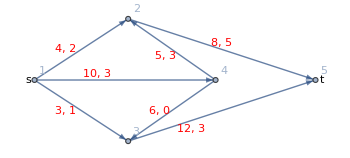

```mathematica
g15=Graph[{2->5,4->2,4->3,1->2,3->5,1->3,1->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{3,-1},{1.4,-1},{0,-2},{-1.5,-1}},EdgeCapacity->{8,5,6,4,1,3,10},EdgeWeight->{5,3,0,2,1,1,3},Epilog->{{Text[Style["s",Medium],{-1.6,-1}]},{Red,Text[Style["3, 1",Medium],{-1,-1.5}]},{Red,Text[Style["10, 3",Medium],{-0.5,-0.9}]},{Red,Text[Style["4, 2",Medium],{-1,-0.5}]},{Red,Text[Style["6, 0",Medium],{0.5,-1.5}]},{Text[Style["t",Medium],{3.1,-1}]},{Red,Text[Style["5, 3",Medium],{0.6,-0.6}]},{Red,Text[Style["8, 5",Medium],{1.5,-0.4}]},{Red,Text[Style["12, 3",Medium],{1,-1.8}]}},ImageSize->350,ImagePadding->20]
```

```mathematica
gdc15=FindMaximumFlow[Graph[{2->5,4->2,4->3,1->2,3->5,1->3,1->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{3,-1},{1.4,-1},{0,-2},{-1.5,-1}},EdgeCapacity->{8,5,6,4,1,3,10},EdgeWeight->{5,3,0,2,1,1,3}],1,5,"OptimumFlowData"]
```

OptimumFlowData[<5>, <6>]

The green cell above contains the value in agreement with the text answer, for the flow. To inventory the contributions and edge structure I go on. The next cell shows what was made available by executing the OptimumFlowData option.

```mathematica
gdc15["Properties"]
```

{CostValue,EdgeList,FlowGraph,FlowMatrix,FlowTable,FlowValue,Properties,ResidualGraph,VertexList}

The flow graph shows all the original edges, but the grid shows that 4->3 is not nonzero.

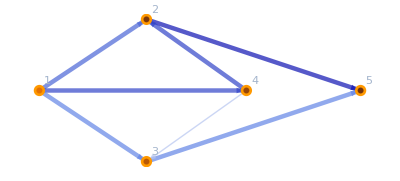

```mathematica
gdc15["FlowGraph"]
```

```mathematica
Grid[{#,gdc15[#]}&/@gdc15["EdgeList"],Frame->All]
```

2->5 | 8
4->2 | 5
3->5 | 1
1->2 | 3
1->3 | 1
1->4 | 5

9.  Problem represented by a diagram.

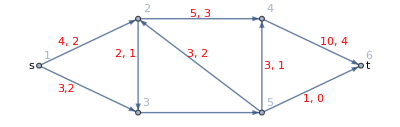

```mathematica
g9=Graph[{1->2,2->4,4->6,3->5,5->6,1->3,5->2,5->4,2->3},VertexLabels->"Name",VertexCoordinates->{{-2,-1},{0,0},{2.5,0},{4.5,-1},{0,-2},{2.5,-2}},EdgeCapacity->{4,5,10,6,1,3,3,3,2},EdgeWeight->{2,3,4,3,0,2,2,1,1},Epilog->{{Text[Style["s",Medium],{-2.15,-1}]},{Red,Text[Style["3,2",Medium],{-1.45,-1.5}]},{Red,Text[Style["3, 1",Medium],{2.75,-1}]},{Red,Text[Style["4, 2",Medium],{-1.4,-0.5}]},{Red,Text[Style["1, 0",Medium],{3.55,-1.7}]},{Text[Style["t",Medium],{4.65,-1}]},{Red,Text[Style["3, 2",Medium],{1.2,-0.75}]},{Red,Text[Style["5, 3",Medium],{1.25,0.1}]},{Red,Text[Style["6, 3",Medium],{1.25,-2.15}]},{Red,Text[Style["10, 4",Medium],{3.95,-0.5}]},{Red,Text[Style["2, 1",Medium],{-0.25,-0.75}]}},ImageSize->400,ImagePadding->35]
```

```mathematica
gdc9=FindMaximumFlow[Graph[{1->2,2->4,4->6,3->5,5->6,1->3,5->2,5->4,2->3},VertexLabels->"Name",VertexCoordinates->{{-2,-1},{0,0},{2.5,0},{4.5,-1},{0,-2},{2.5,-2}},EdgeCapacity->{4,5,10,6,1,3,3,3,2}],1,6,"OptimumFlowData"]
```

OptimumFlowData[<6>, <7>]

The cell above contains the calculated flow value which agrees with the text answer. In the diagram below, two edges do not make contributions, but are shown, I guess, for completeness.

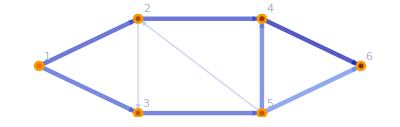

```mathematica
gdc9["FlowGraph"]
```

The grid shows how the flow reaches t.

```mathematica
Grid[{#,gdc9[#]}&/@gdc9["EdgeList"],Frame->All]
```

1->2 | 4
1->3 | 3
2->4 | 4
4->6 | 6
3->5 | 3
5->6 | 1
5->4 | 2

15. Find a minimum cut set in figure 500 and its capacity.

```mathematica
Get["IGraphM`"]
```

IGraph/M 0.3.110 (April 22, 2019)

Evaluate IGDocumentation[] to get started.

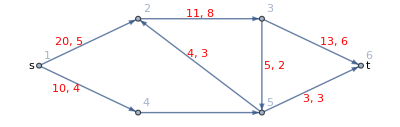

```mathematica
g15=Graph[{1->2,2->3,3->6,4->5,5->6,1->4,5->2,3->5},VertexLabels->"Name",VertexCoordinates->{{-2,-1},{0,0},{2.5,0},{4.5,-1},{0,-2},{2.5,-2}},EdgeCapacity->{20,11,13,7,3,10,4,5},EdgeWeight->{5,8,6,4,3,4,3,2},Epilog->{{Text[Style["s",Medium],{-2.15,-1}]},{Red,Text[Style["10, 4",Medium],{-1.45,-1.5}]},{Red,Text[Style["5, 2",Medium],{2.75,-1}]},{Red,Text[Style["20, 5",Medium],{-1.4,-0.5}]},{Red,Text[Style["3, 3",Medium],{3.55,-1.7}]},{Text[Style["t",Medium],{4.65,-1}]},{Red,Text[Style["4, 3",Medium],{1.2,-0.75}]},{Red,Text[Style["11, 8",Medium],{1.25,0.1}]},{Red,Text[Style["7, 4",Medium],{1.25,-2.15}]},{Red,Text[Style["13, 6",Medium],{3.95,-0.5}]}},ImageSize->400,ImagePadding->35]
```

First I will try out the IG functions. It is necessary to move the EdgeCapacity properties into the EdgeWeight block, because edge weights are what IG will look for in calculating flows.

```mathematica
g15a=Graph[{1->2,2->3,3->6,4->5,5->6,1->4,5->2,3->5},VertexLabels->"Name",VertexCoordinates->{{-2,-1},{0,0},{2.5,0},{4.5,-1},{0,-2},{2.5,-2}},EdgeCapacity->{20,11,13,7,3,10,4,5},EdgeWeight->{20,11,13,7,3,10,4,5},Epilog->{{Text[Style["s",Medium],{-2.15,-1}]},{Red,Text[Style["10, 4",Medium],{-1.45,-1.5}]},{Red,Text[Style["5, 2",Medium],{2.75,-1}]},{Red,Text[Style["20, 5",Medium],{-1.4,-0.5}]},{Red,Text[Style["3, 3",Medium],{3.55,-1.7}]},{Text[Style["t",Medium],{4.65,-1}]},{Red,Text[Style["4, 3",Medium],{1.2,-0.75}]},{Red,Text[Style["11, 8",Medium],{1.25,0.1}]},{Red,Text[Style["7, 4",Medium],{1.25,-2.15}]},{Red,Text[Style["13, 6",Medium],{3.95,-0.5}]}},ImageSize->400,ImagePadding->35]
```

-Graphics-

Then I can call the functions. The IG functions make the same cut as the text answer, and come up with the same flow.

```mathematica
IGMinimumCut[g15a,1,6]
```

{2->3,5->6}

```mathematica
IGMinimumCutValue[g15a,1,6]
```

14.

I still want to take a look at using the Mathematica graph toolset. For this I modify the graph to simply drop the edge weights, since Mathematica will not look at them anyway.

```mathematica
Clear["Global`*"]
```

```mathematica
g155=Graph[{1->2,2->3,3->6,4->5,5->6,1->4,5->2,3->5},VertexLabels->"Name",VertexCoordinates->{{-2,-1},{0,0},{2.5,0},{4.5,-1},{0,-2},{2.5,-2}},EdgeCapacity->{20,11,13,7,3,10,4,5},ImageSize->400,ImagePadding->35];
```

I use FindMaximumFlow with OptimumFlowData so I can get the full menu of available properties. Mathematica reports the maximum flow.

```mathematica
g156=FindMaximumFlow[Graph[{1->2,2->3,3->6,4->5,5->6,1->4,5->2,3->5},VertexLabels->"Name",VertexCoordinates->{{-2,-1},{0,0},{2.5,0},{4.5,-1},{0,-2},{2.5,-2}},EdgeCapacity->{20,11,13,7,3,10,4,5}],1,6,"OptimumFlowData"]
```

OptimumFlowData[<6>, <7>]

I call for an edge list.

```mathematica
g156["EdgeList"]
```

{1->2,1->4,2->3,3->6,4->5,5->6,5->2}

and a flow graph.

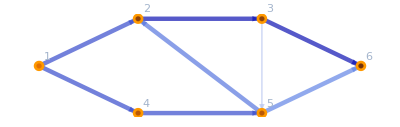

```mathematica
g156["FlowGraph"]
```

I make a grid of the contributing edges and their contributions to the flow. The ghostly edge 3->5 is not represented in the non-zero contribution list. From the grid, I see that I could either cut the graph to get the 14 flow units from 2->3+5->6 or from 1->2+4->5.

```mathematica
Grid[{#,g156[#]}&/@g156["EdgeList"],Frame->All]
```

1->2 | 7
1->4 | 7
2->3 | 11
3->6 | 11
4->5 | 7
5->6 | 3
5->2 | 4

I let Mathematica choose the cut. Mathematica chooses to get the 14 flow from 1->2 + 4->5.

```mathematica
FindMinimumCut[Graph[{1->2,2->3,3->6,4->5,5->6,1->4,5->2,3->5},VertexLabels->"Name",VertexCoordinates->{{-2,-1},{0,0},{2.5,0},{4.5,-1},{0,-2},{2.5,-2}},EdgeCapacity->{20,11,13,7,3,10,4,5}]]
```

{0,{{2,3,6,5},{1,4}}}